### Start choosing the example:

```mathematica
t=27;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,80}},Exit Vertices and Terminal Costs→{{10,15}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.037428,Null}

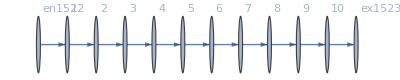

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j1524→80,j1525→80,j1526→80,j1527→80,j1528→80,j1529→80,j1530→80,j1531→80,j1532→80,j1533→80,j1534→80,j1535→0,j1536→0,j1537→0,j1538→0,j1539→0,j1540→0,j1541→0,j1542→0,j1543→0,j1544→0,j1545→0,jt1546→0,jt1547→80,jt1548→80,jt1549→0,jt1550→80,jt1551→0,jt1552→80,jt1553→0,jt1554→80,jt1555→0,jt1556→80,jt1557→0,jt1558→80,jt1559→0,jt1560→80,jt1561→0,jt1562→80,jt1563→0,jt1564→80,jt1565→0,u1566→735,u1567→655,u1568→575,u1569→495,u1570→415,u1571→335,u1572→255,u1573→175,u1574→95,u1575→15,u1576→735,u1577→-80+735,u1578→-80+655,u1579→-80+575,u1580→-80+495,u1581→-80+415,u1582→-80+335,u1583→-80+255,u1584→-80+175,u1585→-80+95,u1586→15,u1587→735|>

```mathematica
Data
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{2,2}},Exit Vertices and Terminal Costs→{{1,4},{3,5}},Switching Costs→{}|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.66454×10^-15

FRX1: The Error on the nonlinear terms is 2.66454×10^-15

<|j1524→80,j1525→80,j1526→80,j1527→80,j1528→80,j1529→80,j1530→80,j1531→80,j1532→80,j1533→80,j1534→80,j1535→0,j1536→0,j1537→0,j1538→0,j1539→0,j1540→0,j1541→0,j1542→0,j1543→0,j1544→0,j1545→0,jt1546→0,jt1547→80,jt1548→80,jt1549→0,jt1550→80,jt1551→0,jt1552→80,jt1553→0,jt1554→80,jt1555→0,jt1556→80,jt1557→0,jt1558→80,jt1559→0,jt1560→80,jt1561→0,jt1562→80,jt1563→0,jt1564→80,jt1565→0,u1566→38.2376,u1567→35.6556,u1568→33.0737,u1569→30.4917,u1570→27.9098,u1571→25.3278,u1572→22.7459,u1573→20.1639,u1574→17.582,u1575→15,u1576→38.2376,u1577→35.6556,u1578→33.0737,u1579→30.4917,u1580→27.9098,u1581→25.3278,u1582→22.7459,u1583→20.1639,u1584→17.582,u1585→15,u1586→15,u1587→38.2376|>

```mathematica
FFR
```

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.06581×10^-14

FRX1: The Error on the nonlinear terms is 1.06581×10^-14

FRX1: The Error on the nonlinear terms is 1.06581×10^-14

«7 more identical outputs»

<|j1524→80,j1525→80,j1526→80,j1527→80,j1528→80,j1529→80,j1530→80,j1531→80,j1532→80,j1533→80,j1534→80,j1535→0,j1536→0,j1537→0,j1538→0,j1539→0,j1540→0,j1541→0,j1542→0,j1543→0,j1544→0,j1545→0,jt1546→0,jt1547→80,jt1548→80,jt1549→0,jt1550→80,jt1551→0,jt1552→80,jt1553→0,jt1554→80,jt1555→0,jt1556→80,jt1557→0,jt1558→80,jt1559→0,jt1560→80,jt1561→0,jt1562→80,jt1563→0,jt1564→80,jt1565→0,u1566→43.4521,u1567→40.2907,u1568→37.1294,u1569→33.968,u1570→30.8067,u1571→27.6454,u1572→24.484,u1573→21.3227,u1574→18.1613,u1575→15,u1576→43.4521,u1577→40.2907,u1578→37.1294,u1579→33.968,u1580→30.8067,u1581→27.6454,u1582→24.484,u1583→21.3227,u1584→18.1613,u1585→15,u1586→15,u1587→43.4521|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.125314

FRX1: The Error on the nonlinear terms is 0.0481351

FRX1: The Error on the nonlinear terms is 0.0175282

FRX1: The Error on the nonlinear terms is 0.00626926

FRX1: The Error on the nonlinear terms is 0.00222951

FRX1: The Error on the nonlinear terms is 0.000791349

FRX1: The Error on the nonlinear terms is 0.000280697

FRX1: The Error on the nonlinear terms is 0.0000995417

FRX1: The Error on the nonlinear terms is 0.0000352969

FRX1: The Error on the nonlinear terms is 0.0000125157

<|j14→0,j15→1.82868,j16→2-1.82868,j17→2-1.82868,j18→2,j19→1.82868,j20→0,j21→0,j22→0,j23→0,jt24→1.82868,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.82868,jt31→2-1.82868,jt32→2-1.82868,jt33→0,u34→4.,u35→4,u36→5.15856,u37→5,u38→5.15856,u39→-0.670121+1. 1.82868+1. 4.,u40→4,u41→-1.98724+1. 1.82868+1. 5.15856,u42→5,u43→5.15856|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1524→80,j1525→80,j1526→80,j1527→80,j1528→80,j1529→80,j1530→80,j1531→80,j1532→80,j1533→80,j1534→80,j1535→0,j1536→0,j1537→0,j1538→0,j1539→0,j1540→0,j1541→0,j1542→0,j1543→0,j1544→0,j1545→0,jt1546→0,jt1547→80,jt1548→80,jt1549→0,jt1550→80,jt1551→0,jt1552→80,jt1553→0,jt1554→80,jt1555→0,jt1556→80,jt1557→0,jt1558→80,jt1559→0,jt1560→80,jt1561→0,jt1562→80,jt1563→0,jt1564→80,jt1565→0,u1566→419.694,u1567→374.728,u1568→329.762,u1569→284.796,u1570→239.83,u1571→194.864,u1572→149.898,u1573→104.932,u1574→59.966,u1575→15,u1576→419.694,u1577→374.728,u1578→329.762,u1579→284.796,u1580→239.83,u1581→194.864,u1582→149.898,u1583→104.932,u1584→59.966,u1585→15,u1586→15,u1587→419.694|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.86107×10^-15

<|j14→0,j15→3/2,j16→2-3/2,j17→2-3/2,j18→2,j19→3/2,j20→0,j21→0,j22→0,j23→0,jt24→3/2,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→3/2,jt31→2-3/2,jt32→2-3/2,jt33→0,u34→4,u35→4,u36→11/2,u37→5,u38→11/2,u39→3/2+4,u40→4,u41→-2+3/2+11/2,u42→5,u43→11/2|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 5.3626×10^-13

FRX1: The Error on the nonlinear terms is 5.3626×10^-13

FRX1: The Error on the nonlinear terms is 5.3626×10^-13

«7 more identical outputs»

<|j1524→80,j1525→80,j1526→80,j1527→80,j1528→80,j1529→80,j1530→80,j1531→80,j1532→80,j1533→80,j1534→80,j1535→0,j1536→0,j1537→0,j1538→0,j1539→0,j1540→0,j1541→0,j1542→0,j1543→0,j1544→0,j1545→0,jt1546→0,jt1547→80,jt1548→80,jt1549→0,jt1550→80,jt1551→0,jt1552→80,jt1553→0,jt1554→80,jt1555→0,jt1556→80,jt1557→0,jt1558→80,jt1559→0,jt1560→80,jt1561→0,jt1562→80,jt1563→0,jt1564→80,jt1565→0,u1566→3290.15,u1567→2926.25,u1568→2562.34,u1569→2198.43,u1570→1834.53,u1571→1470.62,u1572→1106.72,u1573→742.811,u1574→378.906,u1575→15,u1576→3290.15,u1577→2926.25,u1578→2562.34,u1579→2198.43,u1580→1834.53,u1581→1470.62,u1582→1106.72,u1583→742.811,u1584→378.906,u1585→15,u1586→15,u1587→3290.15|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1524→80,j1525→80,j1526→80,j1527→80,j1528→80,j1529→80,j1530→80,j1531→80,j1532→80,j1533→80,j1534→80,j1535→0,j1536→0,j1537→0,j1538→0,j1539→0,j1540→0,j1541→0,j1542→0,j1543→0,j1544→0,j1545→0,jt1546→0,jt1547→80,jt1548→80,jt1549→0,jt1550→80,jt1551→0,jt1552→80,jt1553→0,jt1554→80,jt1555→0,jt1556→80,jt1557→0,jt1558→80,jt1559→0,jt1560→80,jt1561→0,jt1562→80,jt1563→0,jt1564→80,jt1565→0,u1566→205579.,u1567→182739.,u1568→159898.,u1569→137058.,u1570→114217.,u1571→91376.9,u1572→68536.4,u1573→45695.9,u1574→22855.5,u1575→15,u1576→205579.,u1577→182739.,u1578→159898.,u1579→137058.,u1580→114217.,u1581→91376.9,u1582→68536.4,u1583→45695.9,u1584→22855.5,u1585→15,u1586→15,u1587→205579.|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1524→80,j1525→80,j1526→80,j1527→80,j1528→80,j1529→80,j1530→80,j1531→80,j1532→80,j1533→80,j1534→80,j1535→0,j1536→0,j1537→0,j1538→0,j1539→0,j1540→0,j1541→0,j1542→0,j1543→0,j1544→0,j1545→0,jt1546→0,jt1547→80,jt1548→80,jt1549→0,jt1550→80,jt1551→0,jt1552→80,jt1553→0,jt1554→80,jt1555→0,jt1556→80,jt1557→0,jt1558→80,jt1559→0,jt1560→80,jt1561→0,jt1562→80,jt1563→0,jt1564→80,jt1565→0,u1566→2.6104×10^6,u1567→2.32036×10^6,u1568→2.03032×10^6,u1569→1.74027×10^6,u1570→1.45023×10^6,u1571→1.16019×10^6,u1572→870144.,u1573→580101.,u1574→290058.,u1575→15,u1576→2.6104×10^6,u1577→2.32036×10^6,u1578→2.03032×10^6,u1579→1.74027×10^6,u1580→1.45023×10^6,u1581→1.16019×10^6,u1582→870144.,u1583→580101.,u1584→290058.,u1585→15,u1586→15,u1587→2.6104×10^6|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j1524→80,j1525→80,j1526→80,j1527→80,j1528→80,j1529→80,j1530→80,j1531→80,j1532→80,j1533→80,j1534→80,j1535→0,j1536→0,j1537→0,j1538→0,j1539→0,j1540→0,j1541→0,j1542→0,j1543→0,j1544→0,j1545→0,jt1546→0,jt1547→80,jt1548→80,jt1549→0,jt1550→80,jt1551→0,jt1552→80,jt1553→0,jt1554→80,jt1555→0,jt1556→80,jt1557→0,jt1558→80,jt1559→0,jt1560→80,jt1561→0,jt1562→80,jt1563→0,jt1564→80,jt1565→0,u1566→2.6185×10^6,u1567→2.32756×10^6,u1568→2.03661×10^6,u1569→1.74567×10^6,u1570→1.45473×10^6,u1571→1.16379×10^6,u1572→872843.,u1573→581900.,u1574→290958.,u1575→15,u1576→2.6185×10^6,u1577→2.32756×10^6,u1578→2.03661×10^6,u1579→1.74567×10^6,u1580→1.45473×10^6,u1581→1.16379×10^6,u1582→872843.,u1583→581900.,u1584→290958.,u1585→15,u1586→15,u1587→2.6185×10^6|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.03704×10^91

FRX1: The Error on the nonlinear terms is 2.03704×10^91

FRX1: The Error on the nonlinear terms is 2.03704×10^91

«7 more identical outputs»

<|j1524→80,j1525→80,j1526→80,j1527→80,j1528→80,j1529→80,j1530→80,j1531→80,j1532→80,j1533→80,j1534→80,j1535→0,j1536→0,j1537→0,j1538→0,j1539→0,j1540→0,j1541→0,j1542→0,j1543→0,j1544→0,j1545→0,jt1546→0,jt1547→80,jt1548→80,jt1549→0,jt1550→80,jt1551→0,jt1552→80,jt1553→0,jt1554→80,jt1555→0,jt1556→80,jt1557→0,jt1558→80,jt1559→0,jt1560→80,jt1561→0,jt1562→80,jt1563→0,jt1564→80,jt1565→0,u1566→1.98441×10^107,u1567→1.76392×10^107,u1568→1.54343×10^107,u1569→1.32294×10^107,u1570→1.10245×10^107,u1571→8.81959×10^106,u1572→6.61469×10^106,u1573→4.4098×10^106,u1574→2.2049×10^106,u1575→15,u1576→1.98441×10^107,u1577→1.76392×10^107,u1578→1.54343×10^107,u1579→1.32294×10^107,u1580→1.10245×10^107,u1581→8.81959×10^106,u1582→6.61469×10^106,u1583→4.4098×10^106,u1584→2.2049×10^106,u1585→15,u1586→15,u1587→1.98441×10^107|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.79993×10^-10

FRX1: The Error on the nonlinear terms is 4.79993×10^-10

FRX1: The Error on the nonlinear terms is 4.79993×10^-10

«7 more identical outputs»

<|j1524→80,j1525→80,j1526→80,j1527→80,j1528→80,j1529→80,j1530→80,j1531→80,j1532→80,j1533→80,j1534→80,j1535→0,j1536→0,j1537→0,j1538→0,j1539→0,j1540→0,j1541→0,j1542→0,j1543→0,j1544→0,j1545→0,jt1546→0,jt1547→80,jt1548→80,jt1549→0,jt1550→80,jt1551→0,jt1552→80,jt1553→0,jt1554→80,jt1555→0,jt1556→80,jt1557→0,jt1558→80,jt1559→0,jt1560→80,jt1561→0,jt1562→80,jt1563→0,jt1564→80,jt1565→0,u1566→3.0527×10^6,u1567→2.71351×10^6,u1568→2.37432×10^6,u1569→2.03514×10^6,u1570→1.69595×10^6,u1571→1.35676×10^6,u1572→1.01758×10^6,u1573→678389.,u1574→339202.,u1575→15,u1576→3.0527×10^6,u1577→2.71351×10^6,u1578→2.37432×10^6,u1579→2.03514×10^6,u1580→1.69595×10^6,u1581→1.35676×10^6,u1582→1.01758×10^6,u1583→678389.,u1584→339202.,u1585→15,u1586→15,u1587→3.0527×10^6|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.792915

FRX1: The Error on the nonlinear terms is 0.810472

FRX1: The Error on the nonlinear terms is 0.823116

FRX1: The Error on the nonlinear terms is 0.842587

FRX1: The Error on the nonlinear terms is 0.856473

FRX1: The Error on the nonlinear terms is 0.878233

FRX1: The Error on the nonlinear terms is 0.89359

FRX1: The Error on the nonlinear terms is 0.918126

FRX1: The Error on the nonlinear terms is 0.935248

FRX1: The Error on the nonlinear terms is 0.963202

<|j14→0,j15→1.5552,j16→2-1.5552,j17→2-1.5552,j18→2,j19→1.5552,j20→0,j21→0,j22→0,j23→0,jt24→1.5552,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.5552,jt31→2-1.5552,jt32→2-1.5552,jt33→0,u34→4.,u35→4,u36→5.86869,u37→5,u38→5.86869,u39→0.313492+1. 1.5552+1. 4.,u40→4,u41→-2.42388+1. 1.5552+1. 5.86869,u42→5,u43→5.86869|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 5.82077×10^-10

FRX1: The Error on the nonlinear terms is 5.82077×10^-10

FRX1: The Error on the nonlinear terms is 5.82077×10^-10

«7 more identical outputs»

<|j1524→80,j1525→80,j1526→80,j1527→80,j1528→80,j1529→80,j1530→80,j1531→80,j1532→80,j1533→80,j1534→80,j1535→0,j1536→0,j1537→0,j1538→0,j1539→0,j1540→0,j1541→0,j1542→0,j1543→0,j1544→0,j1545→0,jt1546→0,jt1547→80,jt1548→80,jt1549→0,jt1550→80,jt1551→0,jt1552→80,jt1553→0,jt1554→80,jt1555→0,jt1556→80,jt1557→0,jt1558→80,jt1559→0,jt1560→80,jt1561→0,jt1562→80,jt1563→0,jt1564→80,jt1565→0,u1566→4.98931×10^6,u1567→4.43494×10^6,u1568→3.88058×10^6,u1569→3.32621×10^6,u1570→2.77185×10^6,u1571→2.21748×10^6,u1572→1.66311×10^6,u1573→1.10875×10^6,u1574→554381.,u1575→15,u1576→4.98931×10^6,u1577→4.43494×10^6,u1578→3.88058×10^6,u1579→3.32621×10^6,u1580→2.77185×10^6,u1581→2.21748×10^6,u1582→1.66311×10^6,u1583→1.10875×10^6,u1584→554381.,u1585→15,u1586→15,u1587→4.98931×10^6|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.984284

FRX1: The Error on the nonlinear terms is 1.16863

FRX1: The Error on the nonlinear terms is 1.30674

FRX1: The Error on the nonlinear terms is 1.60536

FRX1: The Error on the nonlinear terms is 1.81994

FRX1: The Error on the nonlinear terms is 2.40346

FRX1: The Error on the nonlinear terms is 2.87194

FRX1: The Error on the nonlinear terms is 3.24475

FRX1: The Error on the nonlinear terms is 3.70382

FRX1: The Error on the nonlinear terms is 3.70382

<|j14→0,j15→2.,j16→2-2.,j17→2-2.,j18→2,j19→2.,j20→0,j21→0,j22→0,j23→0,jt24→2.,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2.,jt31→2-2.,jt32→2-2.,jt33→0,u34→4.,u35→4,u36→6.00694,u37→5,u38→6.00694,u39→0.00693559+1. 2.+1. 4.,u40→4,u41→-4.42578+1. 2.+1. 6.00694,u42→5,u43→6.00694|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.53598×10^-8

FRX1: The Error on the nonlinear terms is 1.53598×10^-8

FRX1: The Error on the nonlinear terms is 1.53598×10^-8

«7 more identical outputs»

<|j1524→80,j1525→80,j1526→80,j1527→80,j1528→80,j1529→80,j1530→80,j1531→80,j1532→80,j1533→80,j1534→80,j1535→0,j1536→0,j1537→0,j1538→0,j1539→0,j1540→0,j1541→0,j1542→0,j1543→0,j1544→0,j1545→0,jt1546→0,jt1547→80,jt1548→80,jt1549→0,jt1550→80,jt1551→0,jt1552→80,jt1553→0,jt1554→80,jt1555→0,jt1556→80,jt1557→0,jt1558→80,jt1559→0,jt1560→80,jt1561→0,jt1562→80,jt1563→0,jt1564→80,jt1565→0,u1566→1.40355×10^8,u1567→1.2476×10^8,u1568→1.09165×10^8,u1569→9.357×10^7,u1570→7.7975×10^7,u1571→6.238×10^7,u1572→4.6785×10^7,u1573→3.119×10^7,u1574→1.5595×10^7,u1575→15,u1576→1.40355×10^8,u1577→1.2476×10^8,u1578→1.09165×10^8,u1579→9.357×10^7,u1580→7.7975×10^7,u1581→6.238×10^7,u1582→4.6785×10^7,u1583→3.119×10^7,u1584→1.5595×10^7,u1585→15,u1586→15,u1587→1.40355×10^8|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.24017

FRX1: The Error on the nonlinear terms is 5.07141

FRX1: The Error on the nonlinear terms is 7.05822

FRX1: The Error on the nonlinear terms is 7.05822

FRX1: The Error on the nonlinear terms is 7.05822

«5 more identical outputs»

<|j14→0,j15→2.,j16→2-2.,j17→2-2.,j18→2,j19→2.,j20→0,j21→0,j22→0,j23→0,jt24→2.,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2.,jt31→2-2.,jt32→2-2.,jt33→0,u34→4.,u35→4,u36→6.,u37→5,u38→6.,u39→0.+1. 2.+1. 4.,u40→4,u41→-6.99091+1. 2.+1. 6.,u42→5,u43→6.|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 8255.75

FRX1: The Error on the nonlinear terms is 8255.75

FRX1: The Error on the nonlinear terms is 8255.75

«7 more identical outputs»

<|j1524→80,j1525→80,j1526→80,j1527→80,j1528→80,j1529→80,j1530→80,j1531→80,j1532→80,j1533→80,j1534→80,j1535→0,j1536→0,j1537→0,j1538→0,j1539→0,j1540→0,j1541→0,j1542→0,j1543→0,j1544→0,j1545→0,jt1546→0,jt1547→80,jt1548→80,jt1549→0,jt1550→80,jt1551→0,jt1552→80,jt1553→0,jt1554→80,jt1555→0,jt1556→80,jt1557→0,jt1558→80,jt1559→0,jt1560→80,jt1561→0,jt1562→80,jt1563→0,jt1564→80,jt1565→0,u1566→5.04333×10^19,u1567→4.48296×10^19,u1568→3.92259×10^19,u1569→3.36222×10^19,u1570→2.80185×10^19,u1571→2.24148×10^19,u1572→1.68111×10^19,u1573→1.12074×10^19,u1574→5.6037×10^18,u1575→15,u1576→5.04333×10^19,u1577→4.48296×10^19,u1578→3.92259×10^19,u1579→3.36222×10^19,u1580→2.80185×10^19,u1581→2.24148×10^19,u1582→1.68111×10^19,u1583→1.12074×10^19,u1584→5.6037×10^18,u1585→15,u1586→15,u1587→5.04333×10^19|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 14.698

FRX1: The Error on the nonlinear terms is 20.3268

FRX1: The Error on the nonlinear terms is 20.3268

FRX1: The Error on the nonlinear terms is 20.3268

«16 more identical outputs»

<|j14→0,j15→2.,j16→2-2.,j17→2-2.,j18→2,j19→2.,j20→0,j21→0,j22→0,j23→0,jt24→2.,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2.,jt31→2-2.,jt32→2-2.,jt33→0,u34→4.,u35→4,u36→6.,u37→5,u38→6.,u39→0.+1. 2.+1. 4.,u40→4,u41→-16.3732+1. 2.+1. 6.,u42→5,u43→6.|>

### What we this plot for?

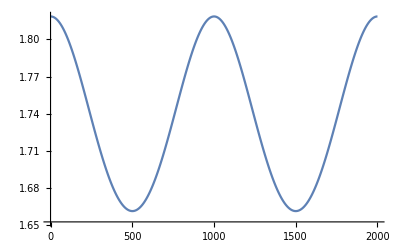

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.